## Fixed overlap

Eigenvalues

The eigenvalues have absolute value given by

```mathematica
λ[q_,t_,n_]:=1/(2q+1)Sum[(n!)/((n/2+h)!(n/2-h)!)Cos[(Pi-t)/2]^(2(n/2+h))Sin[(Pi-t)/2]^(2(n/2-h))CG[q,h,n],{h,Max[-n/2,-q-(n+1)/2],Min[n/2,q-(n+1)/2]}] * WignerCoeff[n,q]
```

with

```mathematica
CG[q_,h_,n_]:=ClebschGordan[{(n+1)/2,(n+1)/2},{n/2,h},{q,(n+1)/2+h}]Conjugate[ClebschGordan[{(n+1)/2,(n+1)/2},{n/2,h},{q,(n+1)/2+h}]]//FullSimplify
```

and we have for C+-

```mathematica
Sqrt[n+2]Sqrt[n]SixJSymbol[{n/2-1/2,n/2,1/2},{n/2+1/2,n/2,q}]//Simplify
```

Piecewise[{{-(ⅈ (-1)^(-n-q) √n √(2+n) √((-1+n)!) √(n!) √((1/2+n-q)!) √((3/2+n+q)!))/(√((1+n)!) √((2+n)!) √((-1/2+n-q)!) √((1/2+n+q)!)), (2 q==1&&n≥1)||(2 q>1&&n≥1/2+q)}, {0, True}}]

so that

```mathematica
WignerCoeff[n_,q_]:=1/2 Sqrt[(2(3/2+q+n)(1/2-q+n))/((n/2+1/2)(n+1))]
```

The strategy is to expand asymptotically first the sum in q and then the sum in h.

Moments of CG distribution

#### Hypergeometric identities

In the following we use the identities, which we check for n=10, h=3

```mathematica
Hypergeometric2F1Regularized[h-n/2,2+2 h+n,3+h+(3 n)/2,-1]== (2^(-2-2 h-n) √π)/(Gamma[2+n] Gamma[1/2 (3+2 h+n)])/.{n->10,h->3}
```

True

```mathematica
h1=(2^(-2-2 h-n) √π)/(Gamma[2+n] Gamma[1/2 (3+2 h+n)])
```

(2^(-2-2 h-n) √π)/(Gamma[2+n] Gamma[1/2 (3+2 h+n)])

```mathematica
Hypergeometric2F1Regularized[1+h-n/2,2+2 h+n,3+h+(3 n)/2,-1]==(2^(-1-2 h-n) √π (1/(Gamma[1+h+n/2] Gamma[3/2+n])-1/(Gamma[1+n] Gamma[1/2 (3+2 h+n)])))/(2 h-n)/.{n->10,h->3}
```

True

```mathematica
h2=(2^(-1-2 h-n) √π (1/(Gamma[1+h+n/2] Gamma[3/2+n])-1/(Gamma[1+n] Gamma[1/2 (3+2 h+n)])))/(2 h-n)
```

(2^(-1-2 h-n) √π (1/(Gamma[1+h+n/2] Gamma[3/2+n])-1/(Gamma[1+n] Gamma[1/2 (3+2 h+n)])))/(2 h-n)

```mathematica
Hypergeometric2F1Regularized[1+h-n/2,3+2 h+n,4+h+(3 n)/2,-1]==(2^(-2-2 h-n) √π (-1/(Gamma[2+h+n/2] Gamma[3/2+n])+1/(Gamma[2+n] Gamma[1/2 (3+2 h+n)])))/(2 h-n)/.{n->10,h->3}
```

True

```mathematica
h3=(2^(-2-2 h-n) √π (-1/(Gamma[2+h+n/2] Gamma[3/2+n])+1/(Gamma[2+n] Gamma[1/2 (3+2 h+n)])))/(2 h-n)
```

(2^(-2-2 h-n) √π (-1/(Gamma[2+h+n/2] Gamma[3/2+n])+1/(Gamma[2+n] Gamma[1/2 (3+2 h+n)])))/(2 h-n)

#### Average

```mathematica
Sum[(2 Gamma[1-h+n/2] Gamma[3/2+h+j+n/2] Gamma[2+n])/(Gamma[1/2-h+j-n/2] Gamma[1+h+n/2] Gamma[3/2-j+n] Gamma[5/2+j+n])j,{j,(n+1)/2+h,n+1/2}]//FullSimplify
```

1/(√π)2^(1+2 h+n) Gamma[3/2+h+n/2] Gamma[2+n] ((1+2 h+n) Hypergeometric2F1Regularized[h-n/2,2+2 h+n,3+h+(3 n)/2,-1]+(-4 h (1+h)+n (2+n)) Hypergeometric2F1Regularized[1+h-n/2,3+2 h+n,4+h+(3 n)/2,-1])

Using the identities

```mathematica
m1=1/(√π)2^(1+2 h+n) Gamma[3/2+h+n/2] Gamma[2+n] ((1+2 h+n) (2^(-2-2 h-n) √π)/(Gamma[2+n] Gamma[1/2 (3+2 h+n)])+(-4 h (1+h)+n (2+n))(2^(-2-2 h-n) √π (-1/(Gamma[2+h+n/2] Gamma[3/2+n])+1/(Gamma[2+n] Gamma[1/2 (3+2 h+n)])))/(2 h-n))//FullSimplify
```

-1/2+(Gamma[3/2+h+n/2] Gamma[2+n])/(Gamma[1+h+n/2] Gamma[3/2+n])

```mathematica
AverageCG[n_,h_]:=-1/2+(Gamma[3/2+h+n/2] Gamma[2+n])/(Gamma[1+h+n/2] Gamma[3/2+n])
```

#### Variance

```mathematica
Sum[(2 Gamma[1-h+n/2] Gamma[3/2+h+j+n/2] Gamma[2+n])/(Gamma[1/2-h+j-n/2] Gamma[1+h+n/2] Gamma[3/2-j+n] Gamma[5/2+j+n])j^2,{j,(n+1)/2+h,n+1/2}]//FullSimplify
```

1/(√π)2^(2 h+n) Gamma[3/2+h+n/2] Gamma[2+n] ((1+2 n (2+2 h+n)) Hypergeometric2F1Regularized[h-n/2,2+2 h+n,3+h+(3 n)/2,-1]-2 (-2 h+n) (2+2 h+n) Hypergeometric2F1Regularized[1+h-n/2,3+2 h+n,4+h+(3 n)/2,-1])

Using the identities

```mathematica
m2=1/(√π)2^(2 h+n) Gamma[3/2+h+n/2] Gamma[2+n] ((1+2 n (2+2 h+n)) (2^(-2-2 h-n) √π)/(Gamma[2+n] Gamma[1/2 (3+2 h+n)])-2 (-2 h+n) (2+2 h+n)(2^(-2-2 h-n) √π (-1/(Gamma[2+h+n/2] Gamma[3/2+n])+1/(Gamma[2+n] Gamma[1/2 (3+2 h+n)])))/(2 h-n))//FullSimplify
```

5/4+h (1+n)+1/2 n (3+n)-(Gamma[3/2+h+n/2] Gamma[2+n])/(Gamma[1+h+n/2] Gamma[3/2+n])

The variance is

```mathematica
5/4+h (1+n)+1/2 n (3+n)-(Gamma[3/2+h+n/2] Gamma[2+n])/(Gamma[1+h+n/2] Gamma[3/2+n])-AverageCG[n,h]^2//FullSimplify
```

1/2 (1+n) (2+2 h+n)-(Gamma[3/2+h+n/2]^2 Gamma[2+n]^2)/(Gamma[1+h+n/2]^2 Gamma[3/2+n]^2)

```mathematica
VarianceCG[n_,h_]:=1/2 (1+n) (2+2 h+n)-(Gamma[3/2+h+n/2]^2 Gamma[2+n]^2)/(Gamma[1+h+n/2]^2 Gamma[3/2+n]^2)
```

#### Skewness

```mathematica
Sum[(2 Gamma[1-h+n/2] Gamma[3/2+h+j+n/2] Gamma[2+n])/(Gamma[1/2-h+j-n/2] Gamma[1+h+n/2] Gamma[3/2-j+n] Gamma[5/2+j+n])j^3,{j,(n+1)/2+h,n+1/2}]//FullSimplify
```

1/(√π)2^(-2+2 h+n) (1+2 h+n) Gamma[1/2+h+n/2] Gamma[2+n] ((1+8 h (-1+n^2)+2 n (5+2 n (3+n))) Hypergeometric2F1Regularized[h-n/2,2+2 h+n,3+h+(3 n)/2,-1]+(2 h-n) (7+n (7+2 n)+h (2+4 n)) Hypergeometric2F1Regularized[1+h-n/2,2+2 h+n,3+h+(3 n)/2,-1])

Using the identities

```mathematica
m3=1/(√π)2^(-2+2 h+n) (1+2 h+n) Gamma[1/2+h+n/2] Gamma[2+n] ((1+8 h (-1+n^2)+2 n (5+2 n (3+n)))h1+(2 h-n) (7+n (7+2 n)+h (2+4 n))h2)//FullSimplify
```

1/8 (-13-12 h (1+n)-6 n (3+n)+(2 (7+n (7+2 n)+h (2+4 n)) Gamma[3/2+h+n/2] Gamma[2+n])/(Gamma[1+h+n/2] Gamma[3/2+n]))

The skewness is

```mathematica
m3-3VarianceCG[n,h]AverageCG[n,h]-AverageCG[n,h]^3//FullSimplify
```

(-(8+2 h (5+4 n)+n (11+4 n)) Gamma[1+h+n/2]^2 Gamma[3/2+n]^2 Gamma[2+n] Gamma[1/2 (3+2 h+n)]+8 Gamma[2+n]^3 Gamma[1/2 (3+2 h+n)]^3)/(4 Gamma[1+h+n/2]^3 Gamma[3/2+n]^3)

```mathematica
(-(8+2 h (5+4 n)+n (11+4 n)) Gamma[1+h+n/2]^2 Gamma[3/2+h+n/2] Gamma[3/2+n]^2 Gamma[2+n]+8 Gamma[3/2+h+n/2]^3 Gamma[2+n]^3)/(4 Gamma[1+h+n/2]^3 Gamma[3/2+n]^3)
```

((-8-2 h (5+4 n)-n (11+4 n)) Gamma[1+h+n/2]^2 Gamma[3/2+h+n/2] Gamma[3/2+n]^2 Gamma[2+n]+8 Gamma[3/2+h+n/2]^3 Gamma[2+n]^3)/(4 Gamma[1+h+n/2]^3 Gamma[3/2+n]^3)

```mathematica
SkewCG[n_,h_]:=(-(8+2 h (5+4 n)+n (11+4 n)) Gamma[1+h+n/2]^2 Gamma[3/2+h+n/2] Gamma[3/2+n]^2 Gamma[2+n]+8 Gamma[3/2+h+n/2]^3 Gamma[2+n]^3)/(4 Gamma[1+h+n/2]^3 Gamma[3/2+n]^3)
```

#### Kurtosis

```mathematica
Sum[(2 Gamma[1-h+n/2] Gamma[3/2+h+j+n/2] Gamma[2+n])/(Gamma[1/2-h+j-n/2] Gamma[1+h+n/2] Gamma[3/2-j+n] Gamma[5/2+j+n])j^4,{j,(n+1)/2+h,n+1/2}]//FullSimplify
```

1/(√π)2^(-2+2 h+n) Gamma[3/2+h+n/2] Gamma[2+n] ((1+16 h^2 n (1+n)+4 n (-1+n+3 n^2+n^3)+8 h (1+n) (3+2 n (1+n))) Hypergeometric2F1Regularized[h-n/2,2+2 h+n,3+h+(3 n)/2,-1]-4 (2 h-n) (5+7 n+2 (h+2 h n+n^2)) Hypergeometric2F1Regularized[1+h-n/2,2+2 h+n,3+h+(3 n)/2,-1])

Using the identities

```mathematica
m4=1/(√π)2^(-2+2 h+n) Gamma[2+n] Gamma[1/2 (3+2 h+n)] ((1+16 h^2 n (1+n)+4 n (-1+n+3 n^2+n^3)+8 h (1+n) (3+2 n (1+n))) h1-4 (2 h-n) (5+7 n+2 (h+2 h n+n^2)) h2)//FullSimplify
```

1/16 (41+16 h^2 n (1+n)+8 h (1+n) (5+2 n (3+n))+4 n (23+n (19+n (7+n)))-(8 (5+7 n+2 (h+2 h n+n^2)) Gamma[3/2+h+n/2] Gamma[2+n])/(Gamma[1+h+n/2] Gamma[3/2+n]))

The kurtosis is

```mathematica
m4-4m3 m1+6m2 m1^2-3 m1^4//FullSimplify
```

1/4 (1+n) (2+2 h+n) (2+n (4+2 h+n))+(-3 Gamma[3/2+h+n/2]^4 Gamma[2+n]^4+2^(-2 (3+2 h+3 n)) (2+2 h (2+n)+n (2+n)) π^2 Gamma[2+2 h+n]^2 Gamma[3+2 n]^2)/(Gamma[1+h+n/2]^4 Gamma[3/2+n]^4)

```mathematica
kurtoCG[n_,h_]:=1/4 (1+n) (4+10 n+4 h^2 n+6 n^2+n^3+4 h (1+3 n+n^2))-(3 Gamma[3/2+h+n/2]^4 Gamma[2+n]^4)/(Gamma[1+h+n/2]^4 Gamma[3/2+n]^4)+(4^(-3-2 h-3 n) (2+2 n+n^2+2 h (2+n)) π^2 Gamma[2+2 h+n]^2 Gamma[3+2 n]^2)/(Gamma[1+h+n/2]^4 Gamma[3/2+n]^4)
```

#### 5th moment

```mathematica
Sum[(2 Gamma[1-h+n/2] Gamma[3/2+h+j+n/2] Gamma[2+n])/(Gamma[1/2-h+j-n/2] Gamma[1+h+n/2] Gamma[3/2-j+n] Gamma[5/2+j+n])j^5,{j,(n+1)/2+h,n+1/2}]//FullSimplify
```

1/(√π)2^(-3+2 h+n) Gamma[3/2+h+n/2] Gamma[2+n] ((1+8 h^2 (1+n) (-1+2 n (-5+2 n))+8 h (1+n) (-9+n (-11+6 n+4 n^2))+2 n (23+n (61+n (61+26 n+4 n^2)))) Hypergeometric2F1Regularized[h-n/2,2+2 h+n,3+h+(3 n)/2,-1]+(2 h-n) (4 h (2+n) (1+2 n) (3+2 n)+4 h^2 (-1+4 n^2)+(1+n) (61+n (71+4 n (7+n)))) Hypergeometric2F1Regularized[1+h-n/2,2+2 h+n,3+h+(3 n)/2,-1])

Using the identities

```mathematica
m5=1/(√π)2^(-3+2 h+n) Gamma[3/2+h+n/2] Gamma[2+n] ((1+8 h^2 (1+n) (-1+2 n (-5+2 n))+8 h (1+n) (-9+n (-11+6 n+4 n^2))+2 n (23+n (61+n (61+26 n+4 n^2)))) h1+(2 h-n) (4 h (2+n) (1+2 n) (3+2 n)+4 h^2 (-1+4 n^2)+(1+n) (61+n (71+4 n (7+n)))) h2)//FullSimplify
```

1/32 (-121-80 h^2 n (1+n)-40 h (1+n) (3+2 n (3+n))-20 n (17+n (17+n (7+n)))+(2 (4 h (2+n) (1+2 n) (3+2 n)+4 h^2 (-1+4 n^2)+(1+n) (61+n (71+4 n (7+n)))) Gamma[3/2+h+n/2] Gamma[2+n])/(Gamma[1+h+n/2] Gamma[3/2+n]))

The 5th moment is

```mathematica
m5-5m4 m1+10m3 m1^2-10 m2 m1^3+4 m1^5//Simplify
```

(-(64+218 n+241 n^2+108 n^3+16 n^4+h^2 (4+80 n+64 n^2)+4 h (19+71 n+64 n^2+16 n^3)) Gamma[1+h+n/2]^4 Gamma[3/2+h+n/2] Gamma[3/2+n]^4 Gamma[2+n]+40 (-2 h+n) Gamma[1+h+n/2]^2 Gamma[3/2+h+n/2]^3 Gamma[3/2+n]^2 Gamma[2+n]^3+64 Gamma[3/2+h+n/2]^5 Gamma[2+n]^5)/(16 Gamma[1+h+n/2]^5 Gamma[3/2+n]^5)

```mathematica
CG5[n_,h_]:=(-(64+218 n+241 n^2+108 n^3+16 n^4+h^2 (4+80 n+64 n^2)+4 h (19+71 n+64 n^2+16 n^3)) Gamma[1+h+n/2]^4 Gamma[3/2+h+n/2] Gamma[3/2+n]^4 Gamma[2+n]+40 (-2 h+n) Gamma[1+h+n/2]^2 Gamma[3/2+h+n/2]^3 Gamma[3/2+n]^2 Gamma[2+n]^3+64 Gamma[3/2+h+n/2]^5 Gamma[2+n]^5)/(16 Gamma[1+h+n/2]^5 Gamma[3/2+n]^5)
```

Moments of the binomial distribution

```mathematica
(n!)/((n/2+h)!(n/2-h)!)Cos[(Pi-t)/2]^(2(n/2+h))Sin[(Pi-t)/2]^(2(n/2-h))
```

(Cos[(π-t)/2]^(2 (h+n/2)) n! Sin[(π-t)/2]^(2 (-h+n/2)))/((-h+n/2)! (h+n/2)!)

is a binomial distribution with probability

```mathematica
(1+r)/2==Cos[(Pi-t)/2]^2
```

We need the rescaled moments for the variable s = 2h/n

```mathematica
b2=CentralMoment[BinomialDistribution[n,(1+r)/2],2]/n^2*4//Simplify
```

(1-r^2)/n

```mathematica
b3=CentralMoment[BinomialDistribution[n,(1+r)/2],3]/n^3*8//Simplify
```

(2 r (-1+r^2))/n^2

```mathematica
b5=CentralMoment[BinomialDistribution[n,(1+r)/2],5]/n^5*32//Simplify
```

-(4 r (-1+r^2) (4-6 r^2+5 n (-1+r^2)))/n^4

```mathematica
b4=CentralMoment[BinomialDistribution[n,(1+r)/2],4]/n^4*16//Simplify
```

((-1+r^2) (2-6 r^2+3 n (-1+r^2)))/n^3

Asymptotic expansion

Expansion for the sum in h

```mathematica
Exph[f_]:=SeriesCoefficient[f,{s,r,0}]+SeriesCoefficient[f,{s,r,2}]b2+SeriesCoefficient[f,{s,r,3}]b3+SeriesCoefficient[f,{s,r,4}]b4
```

The function f has to be expanded around the average value of h, which is nr. To be able to do a final expansion in n, we first express the CG moments in terms of the redefinition h = n s, and take the highest orders in n

```mathematica
Normal[Series[AverageCG[n, n*s/2],{n,Infinity,1},Assumptions->-1<s<1]]//Simplify
```

-1/2+(n √(1+s))/(√2)+(11+5 s)/(8 √2 √(1+s))+(9+14 s-23 s^2)/(128 √2 n (1+s)^(3/2))

```mathematica
Normal[Series[VarianceCG[n, n*s/2],{n,Infinity,1},Assumptions->-1<s<1]]
```

1/8 n (1-s)+(-1+2 s-s^2)/(64 (1+s))+(3-17 s+9 s^2+5 s^3)/(256 n (1+s)^2)

```mathematica
Normal[Series[kurtoCG[n, n*s/2],{n,Infinity,1},Assumptions->-1<s<1]]
```

3/64 n^2 (1-2 s+s^2)+(n (-19+9 s+7 s^2+3 s^3))/(256 (1+s))+(179-428 s+274 s^2+20 s^3-45 s^4)/(4096 (1+s)^2)+(-267+3655 s-2318 s^2-1042 s^3-151 s^4+123 s^5)/(16384 n (1+s)^3)

```mathematica
Series[Expand[SkewCG[n,n*s/2]//FullSimplify],{n,Infinity,1},Assumptions->-1<s<1]
```

((√2-2 √2 s+√2 s^2) n)/(64 √(1+s))+(5 √2+17 √2 s-17 √2 s^2-5 √2 s^3)/(512 (1+s)^(3/2))+(-261 √2-236 √2 s+290 √2 s^2+148 √2 s^3+59 √2 s^4)/(8192 (1+s)^(5/2) n)+O[1/n]^(3/2)

```mathematica
Series[Expand[CG5[n,n*s/2]//FullSimplify],{n,Infinity,1},Assumptions->-1<s<1]
```

(43+4 ((151361 (1+s)^(5/2))/(41472 √2)+1/(36 √2)+4 √2 π^1 (1)+65/3 √2 π^(5/2) ((2305 √(1+s))/(9216 π^(5/2))+(55 2 (-5/1-1))/(48 √2)+(π^(5/2) 1^5 (25/(288 2 1)+275/1+3745/1))/(4 √2)))) n^2+(1) n+(1)+1/n+O[1/n]^(3/2)
 |  |  |  |

Since each derivative in q multiplies the order of the function by a factor of 1/n, in order to get all terms up to order 1/n^2 the moments should be expanded at the following orders:

```mathematica
AverageCGeff[n_,s_]:=-1/2+(n √(1+s))/(√2)+(11+5 s)/(8 √2 √(1+s))+(9+14 s-23 s^2)/(128 √2 n (1+s)^(3/2))
```

```mathematica
VarianceCGeff[n_,s_]:=1/8 n (1-s)+(-1+2 s-s^2)/(64 (1+s))
```

```mathematica
skewCGeff[n_,s_]:=((-1+s)^2 n)/(32 √2 √(1+s))
```

```mathematica
kurtoCGeff[n_,s_]:=3/64 (1-2 s+s^2) n^2
```

Expansion for the sum in q

The sum in h has been transformed into a sum in s, and the moments for the variable s are Θ (1) in n, therefore we can first expand WignerCoeff around the average of CG distribution, expand in powers of 1/n, expand around the average of the rescaled binomial and expand in powers of 1/n again.

```mathematica
Expq[f_]:=SeriesCoefficient[f,{q,AverageCGeff[n,s],0}]+SeriesCoefficient[f,{q,AverageCGeff[n,s],2}]VarianceCGeff[n,s]+SeriesCoefficient[f,{q,AverageCGeff[n,s],3}]skewCGeff[n,s]+SeriesCoefficient[f,{q,AverageCGeff[n,s],4}]kurtoCGeff[n,s]
```

```mathematica
Series[Expq[WignerCoeff[n,q]],{n,Infinity,2}]
```

(√(1-s))/(√2)+(-(3 √(1-s))/(8 √2)+(√(1-s) (-1+s) (1+s)^2)/(√2 (√2+√2 s-2 √(1+s))^2 (√2+√2 s+2 √(1+s))^2))/n+((1+s)^4 (9 √2 √(1-s)-112 √2 √(1-s) s+222 √2 √(1-s) s^2-144 √2 √(1-s) s^3+25 √2 √(1-s) s^4))/(16 (√2+√2 s-2 √(1+s))^4 (√2+√2 s+2 √(1+s))^4 n^2)+O[1/n]^3

```mathematica
Series[Exph[Normal[Series[Expq[WignerCoeff[n,q]],{n,Infinity,2}]]],{n,Infinity,2}]//FullSimplify
```

(√(1-r))/(√2)+(-3+r)/(4 √(2-2 r) n)+(3-5 (-6+r) r)/(32 √(2-2 r) (-1+r) n^2)+O[1/n]^3

```mathematica
Exphtestorder[f_]:=SeriesCoefficient[f,{s,r,0}]+SeriesCoefficient[f,{s,r,2}]b2+SeriesCoefficient[f,{s,r,3}]b3+SeriesCoefficient[f,{s,r,4}]b4+SeriesCoefficient[f,{s,r,5}]b5
```

```mathematica
Exphqestorder[f_]:=SeriesCoefficient[f,{q,AverageCGeff[n,s],0}]+SeriesCoefficient[f,{q,AverageCGeff[n,s],2}]VarianceCGeff[n,s]+SeriesCoefficient[f,{q,AverageCGeff[n,s],3}]skewCGeff[n,s]+SeriesCoefficient[f,{q,AverageCGeff[n,s],4}]kurtoCGeff[n,s]+SeriesCoefficient[f,{q,AverageCGeff[n,s],5}]CG5eff[n,s]
```

```mathematica
Series[Exphtestorder[Normal[Series[Expq[WignerCoeff[n,q]],{n,Infinity,2}]]],{n,Infinity,2}]//FullSimplify
```

(√(1-r))/(√2)+(-3+r)/(4 √(2-2 r) n)+(3-5 (-6+r) r)/(32 √(2-2 r) (-1+r) n^2)+O[1/n]^3

Substitute r->-cos(θ)

```mathematica
(√(1-r))/(√2)+(-3+r)/(4 √(2-2 r) n)+(3-5 (-6+r) r)/(32 √(2-2 r) (-1+r) n^2)+O[1/n]^3/.{r->-Cos[Θ]}//FullSimplify
```

√(Cos[Θ/2]^2)+(-3-Cos[Θ])/(4 √(2+2 Cos[Θ]) n)+(-1+60 Cos[Θ]+5 Cos[2 Θ])/(64 √2 (1+Cos[Θ])^(3/2) n^2)+O[1/n]^3

and finally

```mathematica
Pasy[n_,θ_]:=1/2(1-(√(Cos[Θ/2]^2)+(-3-Cos[Θ])/(4 √(2+2 Cos[Θ]) n)+(-1+60 Cos[Θ]+5 Cos[2 Θ])/(64 √2 (1+Cos[Θ])^(3/2) n^2)))
```

Perr

In general the error probability is

```mathematica
Perr[n_,t_]:=1/2(1-Sum[(2q+1)λ[q,t,n],{q,1/2,n-1/2}])
```

Final result

```mathematica
Pasy[n_,θ_]:=1/2(1-(√(Cos[Θ/2]^2)+(-3-Cos[Θ])/(4 √(2+2 Cos[Θ]) n)+(-1+60 Cos[Θ]+5 Cos[2 Θ])/(64 √2 (1+Cos[Θ])^(3/2) n^2)))
```

Check with average over overlap r

```mathematica
1/2(1-((√(1-r))/(√2)+(-3+r)/(4 √(2-2 r) n)))/.{r->2c-1}//FullSimplify
```

(2+4 (-1+√(1-c)) n+c (-1+4 n))/(8 √(1-c) n)

```mathematica
Series[FullSimplify[Integrate[(2+4 (-1+√(1-c)) n+c (-1+4 n))/(8 √(1-c) n)(d-1)(1-c)^(d-2),{c,0,1}],Assumptions->d∈Integers && d>3],{n,Infinity,1}]
```

1/(2 (-1+2 d))+(1-2 d+d^2)/((3-8 d+4 d^2) n)+O[1/n]^2

```mathematica
Pasy[n_,Θ_]:=1/2(1-(√(Cos[Θ/2]^2)+(-3-Cos[Θ])/(4 √(2+2 Cos[Θ]) n)+(-1+60 Cos[Θ]+5 Cos[2 Θ])/(64 √2 (1+Cos[Θ])^(3/2) n^2)))
```

```mathematica
Pasy2nd[n_,Θ_]:=-1/2((-1+60 Cos[Θ]+5 Cos[2 Θ])/(64 √2 (1+Cos[Θ])^(3/2) n^2))
```

#### Plot

Plot for θ=pi/3,

```mathematica
Perrexactlist=Table[{n,Perr[n,Pi/3]},{n,5,30,5}]//N
```

{{5.,0.119571},{10.,0.091931},{15.,0.0835678},{20.,0.0794522},{25.,0.0769802},{30.,0.0753279}}

```mathematica
Perrexactlist2nd=Table[{n,Perr[n,Pi/3]-1/2(1-(√(Cos[(Pi/3)/2]^2)+(-3-Cos[Pi/3])/(4 √(2+2 Cos[Pi/3]) n)))},{n,30,70,5}]//N
```

{{30.,-0.0000790592},{35.,-0.0000591724},{40.,-0.000045909},{45.,-0.0000366377},{50.,-0.0000299085},{55.,-0.0000248728},{60.,-0.0000210075},{65.,-0.0000179767},{70.,-0.0000155568}}

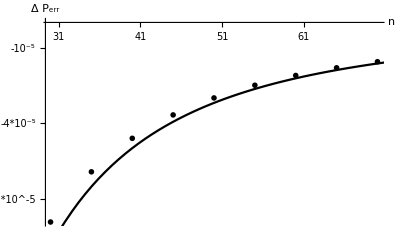

```mathematica
order2=Show[ListPlot[Perrexactlist2nd,PlotTheme->"Monochrome"],Plot[Pasy2nd[n,Pi/3],{n,31,71},PlotTheme->"Monochrome"],AxesLabel->{n,Δ Subscript[P, err]},Ticks->{{31,41,51,61,71},{{-10^-5,"-10^-5"},{-4*10^-5,"-4*10^-5 "},{-7*10^-5,"-7*10^-5"}}}]
```

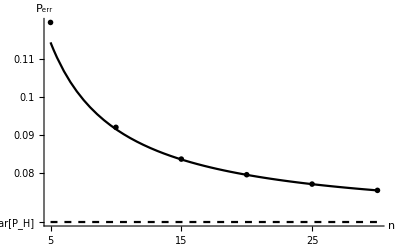

```mathematica
angleplot=Show[ListPlot[Perrexactlist,PlotTheme->"Monochrome"],Plot[Pasy[n,Pi/3],{n,5,30},PlotTheme->"Monochrome"],
Plot[1/2(1-(√(Cos[Pi/6]^2))),{n,5,30},PlotTheme->"Monochrome",PlotStyle->Dashed],Epilog->Inset[order2,{23,0.105}],AxesLabel->{Style["n",Medium],Style["P_err",Medium]},PlotRange->All,AxesOrigin->{4.5,0.06}, Ticks->{{5,10,15,20,25,30},{{1/2(1-(√(Cos[Pi/6]^2))),OverBar["P_H"]},0.08,0.09,0.10,0.11}}]
```

Average on the overlap, alternative derivation

The dimension of the totally symmetric representation  in the product of n d-level systems is

```mathematica
dim[d_,n_]:=Binomial[n+d-1,d-1]
```

The dimension of a representation with two rows in the product of (n+1)*n d - level systems is

```mathematica
dim2[d_,n_,r_]:=Binomial[2+2 n,1+n+r] Pochhammer[-1+d,-r+ n+1] Pochhammer[d,n+r]/(2n+2)!(2r)
```

where r is the lenght of the first row -n

The total probability of error is

```mathematica
Perrd[n_,d_]:=1/2(1-Sum[WignerCoeff[n,r-1/2]/(dim[d,n]dim[d,n+1])dim2[d,n,r],{r,1,n}])
```

First of all we expand asymptotically the integrand

```mathematica
Series[ WignerCoeff[n,n*s-1/2]/(dim[d,n]dim[d,n+1])dim2[d,n,n*s],{n,Infinity,2},Assumptions->0<s<1]
```

(2 (-1+d)^2 (1-s)^d s (1+s)^(-2+d) √(1-s^2) Gamma[-1+d])/((-1+s)^2 Gamma[d] n)-(2 ((-1+d)^2 (1-s)^d s (1+s)^(-3+d) √(1-s^2) (-1-d+d^2 s^2) Gamma[-1+d]))/(((-1+s)^3 Gamma[d]) n^2)+O[1/n]^3

Then we use Euler-McLaurin approximation

```mathematica
n*Integrate[(2 (-1+d)^2 (1-s)^d s (1+s)^(-2+d) √(1-s^2) Gamma[-1+d])/((-1+s)^2 Gamma[d] n)-(2 ((-1+d)^2 (1-s)^d s (1+s)^(-3+d) √(1-s^2) (-1-d+d^2 s^2) Gamma[-1+d]))/(((-1+s)^3 Gamma[d]) n^2),{s,0,1}]
```

ConditionalExpression[(2 (-1+d) (1-3 n+d (-1+2 n)))/((3+4 (-2+d) d) n),Re[d]>3/2]

So that we wave finally

```mathematica
FullSimplify[Series[1/2((2 (-1+d) (1-3 n+d (-1+2 n)))/((3+4 (-2+d) d) n)),{n,Infinity,1}],Assumptions->d>3&&d∈Integers]
```

(-1+d)/(-1+2 d)-(-1+d)^2/((3+4 (-2+d) d) n)+O[1/n]^2